```mathematica
Needs["queues`"]
```

```mathematica
RandExp[x_]:=-1/x*Log[Random[Real]];
```

# Practica 1

## M/M/1

Estado del sistema

```mathematica
mm1 = Queue1Sim[RandExp[10],RandExp[11],10000];
```

```mathematica
statemm1 = Stire[StateTime[mm1]];
```

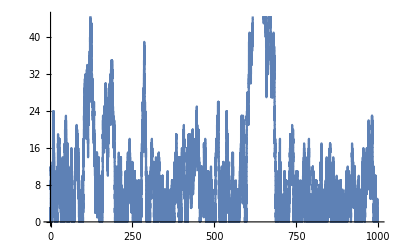

```mathematica
ListLinePlot[statemm1]
```

```mathematica
Manipulate[ListLinePlot[statemm1[[origen;;origen+with]]],{origen,1,Length[statemm1],1},{with,10,1000,1}]
```

Tiempo medio de espera en el sistema

```mathematica
NormalizedMean1[ros_,mu_]:=Map[{#,MeanSystemTime[Queue1Sim[RandExp[mu*#],RandExp[mu],10000]]*mu}&,ros]
```

```mathematica
ros={0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1};
```

```mathematica
Experimentalmean1 = NormalizedMean1[ros,15];
```

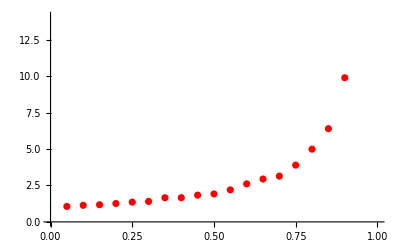

```mathematica
g11 = ListPlot[Experimentalmean1,PlotStyle->Red]
```

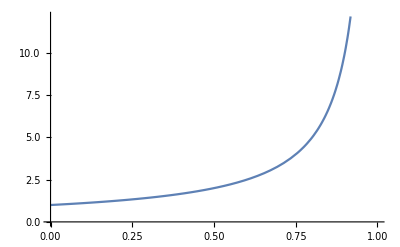

```mathematica
g21 = Plot[1/(1-ro),{ro,0,1},AxesOrigin->{0,0}]
```

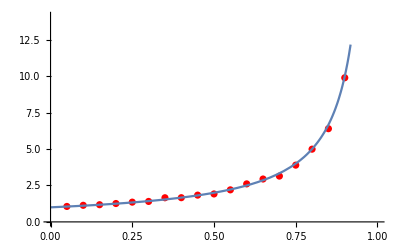

```mathematica
Show[g11,g21]
```

Probabilidad de estado en el sistema

```mathematica
StatusProbTeo1[nstates_,ro_]:=Map[{#,(1-ro)*ro^(#)}&,NestWhileList[(#+1)&,0,(#<nstates)&]]
```

```mathematica
spTeo=StatusProbTeo1[54,10/11//N];
```

```mathematica
ProbSim=Queue1Sim[RandExp[10],RandExp[11],10000];
```

```mathematica
spPasta=StatusProbPasta[ProbSim];
```

```mathematica
spTime=StatusProbTime[ProbSim];
```

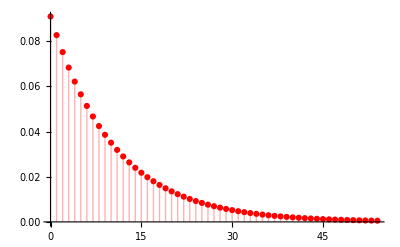

```mathematica
p1=ListPlot[spTeo,PlotStyle->Red,Filling->Axis]
```

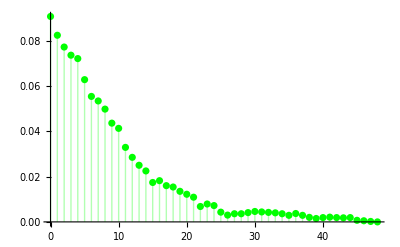

```mathematica
p2=ListPlot[spPasta,PlotStyle->Green,Filling->Axis]
```

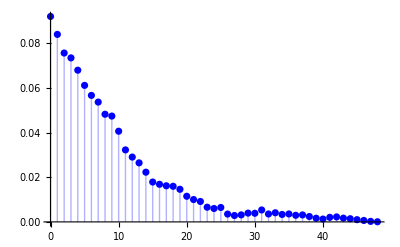

```mathematica
p3=ListPlot[spTime,PlotStyle->Blue,Filling->Axis]
```

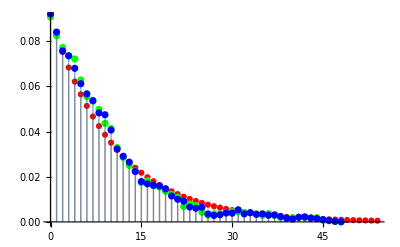

```mathematica
Show[p1,p2,p3]
```

## M/M/2

Estado del sistema

```mathematica
mm2=Queue2Sim[RandExp[10],RandExp[11],10000];
```

```mathematica
statemm2 = Stire[StateTime[mm2]];
```

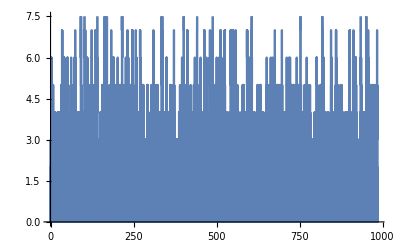

```mathematica
ListLinePlot[statemm2]
```

```mathematica
Manipulate[ListLinePlot[statemm2[[origen;;origen+with]]],{origen,1,Length[statemm2],1},{with,10,1000,1}]
```

Tiempo medio de estado en el sistema

```mathematica
NormalizedMean2[ros_,mu_]:=Map[{#,MeanSystemTime[Queue2Sim[RandExp[2*mu*#],RandExp[mu],10000]]*mu}&,ros]
```

```mathematica
Experimentalmean2 = NormalizedMean2[ros,15];
```

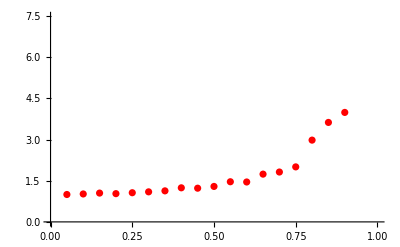

```mathematica
g12 = ListPlot[Experimentalmean2,PlotStyle->Red]
```

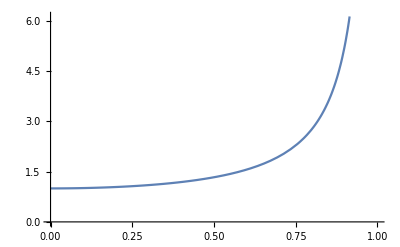

```mathematica
g22 = Plot[1/(1-ro^2),{ro,0,1},AxesOrigin->{0,0}]
```

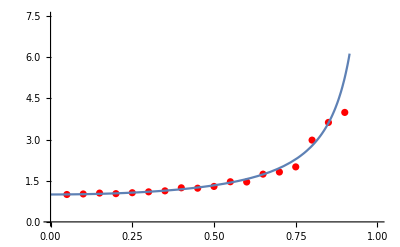

```mathematica
Show[g12,g22]
```

Probabilidad de estado en el sistema

```mathematica
StatusProbTeo2[nstates_,ro_]:=Map[{#,If[#==0,(1-ro)/(1+ro),(2*(1-ro)/(1+ro))*ro^(#)]}&,NestWhileList[(#+1)&,0,(#<nstates)&]]
```

```mathematica
Comprobar[x_]:=Total[Map[#[[2]]&,x]]
```

```mathematica
spTeo2=StatusProbTeo2[20,10/22//N]
```

{{0,0.375},{1,0.340909},{2,0.154959},{3,0.0704358},{4,0.0320163},{5,0.0145528},{6,0.00661493},{7,0.00300679},{8,0.00136672},{9,0.000621237},{10,0.00028238},{11,0.000128355},{12,0.000058343},{13,0.0000265196},{14,0.0000120543},{15,5.47925×10^-6},{16,2.49057×10^-6},{17,1.13208×10^-6},{18,5.1458×10^-7},{19,2.339×10^-7},{20,1.06318×10^-7}}

```mathematica
Comprobar[spTeo2]
```

1.

```mathematica
ProbSim2=Queue2Sim[RandExp[10],RandExp[11],10000];
```

```mathematica
spPasta2=StatusProbPasta[ProbSim2]
```

{{0,0.371963},{1,0.338866},{2,0.151785},{3,0.0735926},{4,0.0352965},{5,0.0172983},{6,0.0069993},{7,0.00239976},{8,0.00089991},{9,0.00049995},{10,0.00009999},{11,0.00009999},{12,0.00009999},{13,0.00009999},{14,0.}}

```mathematica
Comprobar[spPasta2]
```

1.

```mathematica
spTime2=StatusProbTime[ProbSim2];
```

$Aborted

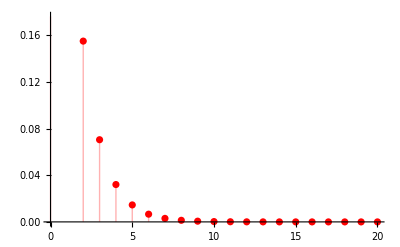

```mathematica
p12=ListPlot[spTeo2,PlotStyle->Red,Filling->Axis]
```

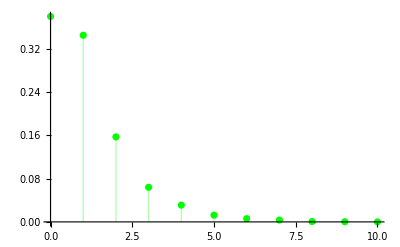

```mathematica
p22=ListPlot[spPasta2,PlotStyle->Green,Filling->Axis]
```

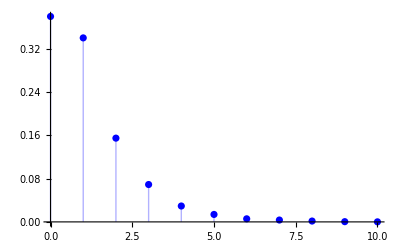

```mathematica
p32=ListPlot[spTime2,PlotStyle->Blue,Filling->Axis]
```

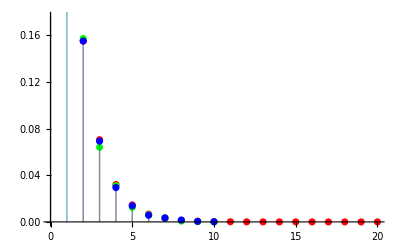

```mathematica
Show[p12,p22,p32]
```

## M/M/1N

Estado del sistema

```mathematica
mm1n=Queue1NSim[RandExp[10],RandExp[11],10000,6];
```

```mathematica
statemm1n = Stire[StateTime[mm1n]];
```

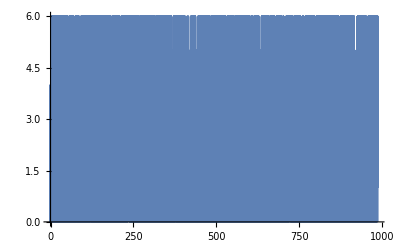

```mathematica
ListLinePlot[statemm1n]
```

```mathematica
Manipulate[ListLinePlot[statemm1n[[origen;;origen+with]]],{origen,1,Length[statemm1n],1},{with,10,1000,1}]
```

Tiempo medio de estado en el sistema

```mathematica
NormalizedMean1N[ros_,mu_]:=Map[{#,MeanSystemTime[Queue1NSim[RandExp[mu*#],RandExp[mu],10000,6]]*mu}&,ros]
```

```mathematica
Experimentalmean1N = NormalizedMean1N[ros,15]
```

{{0.05,1.05862},{0.1,1.10301},{0.15,1.17119},{0.2,1.23792},{0.25,1.30864},{0.3,1.40757},{0.35,1.53336},{0.4,1.65596},{0.45,1.74983},{0.5,1.89275},{0.55,2.09227},{0.6,2.29136},{0.65,2.44263},{0.7,2.51612},{0.75,2.75263},{0.8,2.88908},{0.85,3.08797},{0.9,3.14555},{0.95,3.37263},{1,3.49026}}

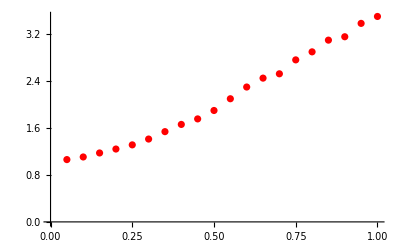

```mathematica
g12 = ListPlot[Experimentalmean1N,PlotStyle->Red]
```

```mathematica
g22 = Plot[1/(1-ro^2),{ro,0,1},AxesOrigin->{0,0}]
```